```mathematica
ClearAll[t,kvadrati]

t[{x_,y_}]:={(1-y)/2,(x+1)/2}
t[Line[xs_]]:=Line[t/@xs]

kvadrati[0]:={}
kvadrati[n_]:=
Prepend[t/@kvadrati[n-1],Line[{{-1,-1},{1,-1},{1,1},{-1,1},{-1,-1}}]]
```

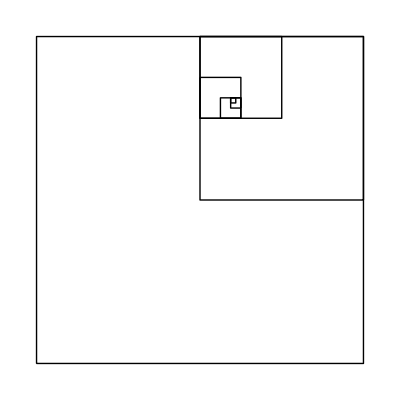

```mathematica
pic=kvadrati[7]//Graphics
```